```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
Elements = Import["elements.txt","Table","FieldSeparators"->","];
Nodes = Import["nodes.txt","Table","FieldSeparators"->","];
```

```mathematica
Nodes = Drop[Nodes, None, {1}];(*odstrani prvi stolpec*)
Elements = Drop[Elements, None, {1}];
```

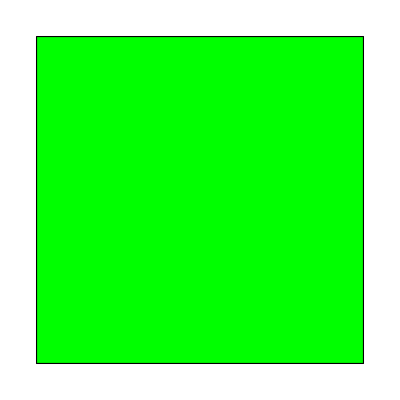

```mathematica
(*Vizulaizacija elementov*)
ELplot= Table[{
	Graphics[{Green,EdgeForm[Black],Polygon[Nodes[[Elements[[i]]]]]}]},
	{i,1,Length[Elements]}];
Show[ELplot]
```

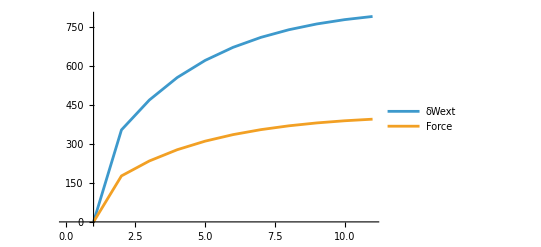

```mathematica
(*Force*)
Force = Import["sila.txt", "Table", HeaderLines -> 3][[1;;-5,2]];
T = Import["sila.txt", "Table", HeaderLines -> 3][[1;;-5,1]];
U = Import["pomik.txt", "Table", HeaderLines -> 3][[1;;-5, 2]];
Nap = Import["stress.txt", "Table", HeaderLines -> 4][[1;;-5, 2;;4]];
δWext = 2 * Force;
ListLinePlot[{δWext, Force}, AxesOrigin->{1,0}, PlotLegends->{"δWext","Force"}]
```

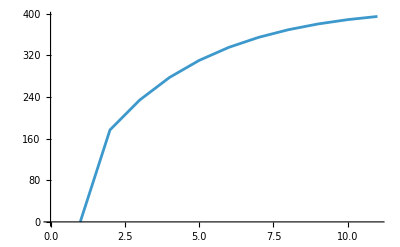

```mathematica
FJSON = Import["Grad_1_PHANTOM.json","RawJSON"];
F  = {{1,0,0,1, 1}};
(*Napetosti iz Abaqus simulacije*)
σ11 = Nap[[;;,1]]; (*Prvi stolpec*)
σ12 = Nap[[;;,2]]; (*Drugi stolpec*)
σ22 = Nap[[;;,3]] ;
```

```mathematica
For[frame=1, frame <= 10, frame++,

(*FJSON[frame][element][Gauss Integration Point][Variable -> x,y,F]*)
(*F = FJSON[ToString[frame]]["1"]["1"]["F"];
Print[F];


(*Gradient*)
(*Stolpci -> UVARM-4.for*)
F11 = F[[1]];
F12 = F[[2]];
F21 = F[[3]];
F22 = F[[4]];
F33 = F[[5]];

(*1. Piola-Kirchoff Stress -> p*)
p11 = F33 (F22 σ11 - F12 σ12);
p12 = - F21 F33 σ11 + F11 F33 σ12;
p21 = F33 (F22 σ12 - F12 σ22);
p22 = -F21 F22 σ12 + F11 F33 σ22;*)

(*Jacobian matrix*)
(*Mapping the determinant*)
Subscript[𝒯, 1] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {-1,-1};
Subscript[𝒯, 2] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {1,-1};
Subscript[𝒯, 3] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {1,1};
Subscript[𝒯, 4] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {-1,1};
Subscript[ψ, i_][𝒳_, 𝒴_] := 1/4(1 + Subscript[𝒯, i][[1]] * 𝒳) *(1 + Subscript[𝒯, i][[2]]  * 𝒴);

(*Only one element now*)
det = {};

For[j =1, j <= Length[Elements], j++,
	x = Nodes[[Elements[[j]]]][[;;,1]];
	y = Nodes[[Elements[[j]]]][[;;,2]];

	X[𝒳_, 𝒴_]  := Sum[Subscript[ψ, i][𝒳, 𝒴] x[[i]],{i,1,4}];
	Y[𝒳_, 𝒴_]  := Sum[Subscript[ψ, i][𝒳, 𝒴] y[[i]],{i,1,4}];
	J[𝒳_, 𝒴_]  = ({{D[X[𝒳, 𝒴], 𝒳], D[Y[𝒳, 𝒴], 𝒳]}, {D[X[𝒳, 𝒴], 𝒴], D[Y[𝒳, 𝒴], 𝒴]}});
	(*J[𝒳_, 𝒴_] = ({{D[X[𝒳, 𝒴],𝒳], D[Y[𝒳, 𝒴],𝒳]}, {D[X[𝒳, 𝒴],𝒴], D[Y[𝒳, 𝒴],𝒴]}});*)
];

det = Append[det,
{
Det[J[-1/(√3),-1/(√3)]],
Det[J[1/(√3),-1/(√3)]],
Det[J[-1/(√3),1/(√3)]],
Det[J[1/(√3),1/(√3)]]
}
];
	
δWint = {0};
For[i = 1, i <= Length[Elements],i++, (*element*)
		For[j=1, j <= 4, j++,(*Gaussova tocka*)
						(*FJSON[frame][element][Gauss Integration Point][Variable -> x,y,F]*)
			F = FJSON[ToString[frame]][ToString[i]][ToString[j]]["F"];
			(*Print[F];*)
			
			
			(*Gradient*)
			(*Stolpci -> UVARM-4.for*)
			F11 = F[[1]];
			F12 = F[[2]];
			F21 = F[[3]];
			F22 = F[[4]];
			F33 = F[[5]];
			
			(*1. Piola-Kirchoff Stress -> p*)
			p11 = F33 (F22 σ11 - F12 σ12);
			p12 = - F21 F33 σ11 + F11 F33 σ12;
			p21 = F33 (F22 σ12 - F12 σ22);
			p22 = -F21 F22 σ12 + F11 F33 σ22;
			
			δWinti = (p11 F11 + p12 F12 + p21 F21 + p22 F22) *det[[1,j]];
			Print[δWinti];
		]
	
]
];
```

{0.,48.5653,70.2112,90.1194,108.548,125.705,141.754,156.83,171.044,184.489,197.245}

{0.,48.5653,70.2112,90.1194,108.548,125.705,141.754,156.83,171.044,184.489,197.245}

{0.,48.5653,70.2112,90.1194,108.548,125.705,141.754,156.83,171.044,184.489,197.245}

«37 more identical outputs»

```mathematica
det[[1,1]]
```

0.25